```mathematica
MatrixForm[Table[0,{i,4},{j,4}]]
```

```mathematica
HAM[kx_,ky_,t1_,t2_]:=({{0, t1(1+Exp[-I kx ]), t2, t1(1+Exp[I ky])}, {t1(1+Exp[I kx]), 0, t1(1+Exp[I ky]), t2 Exp[I kx+I ky]}, {t2, t1(1+Exp[-I ky]), 0, t1(1+Exp[I kx])}, {t1(1+Exp[-I ky]), t2 Exp[-I kx-I ky], t1(1+Exp[-I kx]), 0}})
```

```mathematica
ENERGY[kx_,ky_,t1_,t2_]:=Sort[Eigenvalues[HAM[kx,ky,t1,t2]]]
```

```mathematica
FSSL[kx_,ky_]:=ENERGY[kx,ky,-1,-2.5]
```

```mathematica
Plot3D[FSSL[x,y],{x,-Pi,Pi},{y,-Pi,Pi},ColorFunction->Function[{x,y,z},Hue[z]]]
```

-Graphics3D-

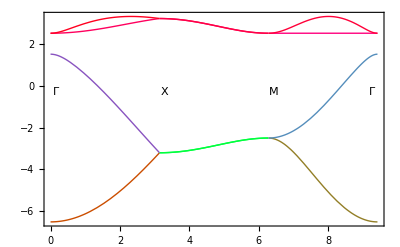

```mathematica
Plot[Piecewise[{{FSSL[t,0],t≥0&&t≤Pi},{FSSL[Pi,t-Pi],t>Pi&&t≤2Pi},{FSSL[Pi-(t-2Pi),Pi-(t-2Pi)],t>2Pi&&t≤3Pi}}],{t,0,3Pi},GridLines->{{{0,Dashed},{Pi,Dashed},{2Pi,Dashed},{3Pi,Dashed}},{}},Epilog->{Inset["Γ",{0.15,-0.28}],Inset["X",{Pi+0.15,-0.28}],Inset["M",{2Pi+0.15,-0.28}],Inset["Γ",{3Pi-0.15,-0.28}]},Frame->True,ColorFunction->Function[{x,y},Hue[y]]]
```

```mathematica
ENERGY[0,0,-1,-2.5]
```

{-6.5,1.5,2.5,2.5}

```mathematica
CON=Table[0,{i,24},{j,24}];
```

```mathematica
Clear[CCor]
```

```mathematica
CCor[kx_]:=(Cc=CON;Clear[Cor];Cor=CON;For[i=1,i≤6,i++,For[j=1,j≤6,j++,For[l=1,l≤4,l++,For[m=1,m≤4,m++,Cor[[4(i-1)+l]][[4(j-1)+m]]=Integrate[Exp[-I(i-j)ky]HAM[kx,ky,-1,-2.5][[l]][[m]],{ky,-Pi,Pi}]]]]];For[i=1,i≤24,i++,For[j=1,j≤24,j++,Cc[[i]][[j]]=Cor[[i]][[j]]]];Cc)
```

```mathematica
DR[kx_]:=Sort[Re[Eigenvalues[N[CCor[kx]]]]]
```

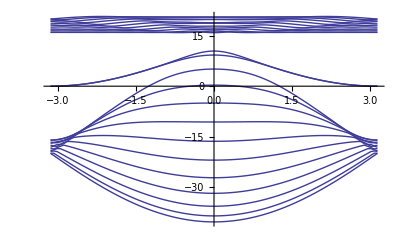

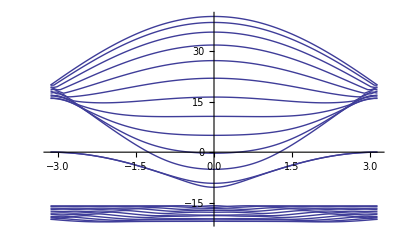

```mathematica
DiscretePlot[DR[kx],{kx,-Pi,Pi,2Pi/100},Filling->None,Evaluate[Joined->True],ColorFunction->"Rainbow"]
```

### odd lattice

```mathematica
CON=Table[0,{i,20},{j,20}];
```

```mathematica
Clear[CCor]
```

```mathematica
CCor[kx_]:=(Cc=CON;Clear[Cor];Cor=CON;For[i=1,i≤5,i++,For[j=1,j≤5,j++,For[l=1,l≤4,l++,For[m=1,m≤4,m++,Cor[[4(i-1)+l]][[4(j-1)+m]]=Integrate[Exp[-I(i-j)ky]HAM[kx,ky,1,2.5][[l]][[m]],{ky,-Pi,Pi}]]]]];For[i=1,i≤20,i++,For[j=1,j≤20,j++,Cc[[i]][[j]]=Cor[[i]][[j]]]];Cc)
```

```mathematica
DR[kx_]:=Sort[Re[Eigenvalues[N[CCor[kx]]]]]
```

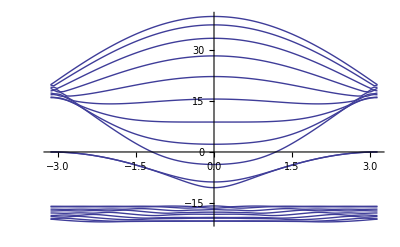

```mathematica
DiscretePlot[DR[kx],{kx,-Pi,Pi,2Pi/100},Filling->None,Evaluate[Joined->True]]
```

### Entanglement spectrum,

```mathematica
ESYs[kx_,ky_]:=Eigensystem[HAM[kx,ky,-1,-2.5]]
```

```mathematica
ESYs[1,1]
```

{{-5.75689,3.20157,2.5,0.0553184},{{-0.35848-0.360177 ⅈ,0.00232178-0.491691 ⅈ,-0.35848-0.360177 ⅈ,-0.491696},{0.250299-0.0911552 ⅈ,-0.501609+0.421224 ⅈ,0.250299-0.0911552 ⅈ,-0.655012},{-0.687213-0.166548 ⅈ,9.71445×10^-17+2.08167×10^-17 ⅈ,0.687213+0.166548 ⅈ,0.},{-0.0214621-0.412729 ⅈ,-0.57066+0.0595101 ⅈ,-0.0214621-0.412729 ⅈ,0.573754}}}

```mathematica
ESYs[1,1][[2]][[1]]
```

{-0.35848-0.360177 ⅈ,0.00232178-0.491691 ⅈ,-0.35848-0.360177 ⅈ,-0.491696}

```mathematica
VEc[kx_,ky_]:=(Clear[VEc1,VEc2];For[i=1;j=1,i≤4,i++,If[ESYs[kx,ky][[1]][[i]]<2,If[j==1,VEc1=ESYs[kx,ky][[2]][[i]];j++,VEc2=ESYs[kx,ky][[2]][[i]]]]];{VEc1,VEc2})
```

```mathematica
VEc[0,0]
```

{{0.5,0.5,0.5,0.5},{0.5,-0.5,0.5,-0.5}}

```mathematica
Plot3D[Re[VEc[kx,ky][[2]]],{kx,-Pi,Pi},{ky,-Pi,Pi}]
```

-Graphics3D-

```mathematica
INT[y_,kx_,LL_,HL_,i_,j_]:=(Clear[int];
For[ii=LL;int=0,ii≤HL,ii=ii+0.05,int+=0.05y[kx,ii,i,j]];int)
```

```mathematica
CORe[kx_,ky_,i_,j_]:=Exp[I (i-j) ky](KroneckerProduct[Conjugate[VEc[kx,ky][[1]]],VEc[kx,ky][[1]]]+KroneckerProduct[Conjugate[VEc[kx,ky][[2]]],VEc[kx,ky][[2]]])
```

```mathematica
HCOr[kx_]:=(Clear[COR];Clear[OUT];OUT=Table[COR[i][j],{i,6},{j,6}];For[iii=1,iii≤6,iii++,For[jjj=1,jjj≤6,jjj++,COR[iii][jjj]=INT[CORe,kx,-Pi,Pi,iii,jjj]]];OUT=ArrayFlatten[OUT])
```

```mathematica
MatrixForm[N[HCOr[1]]]
```

(3.14999+0. ⅈ | 0.95547+0.521945 ⅈ | 2.56526-0.378173 ⅈ | 0.443196+0.472733 ⅈ | -0.00839667+0.201302 ⅈ | -0.748071-0.408734 ⅈ | 0.270083-0.262999 ⅈ | 0.140864+0.0767881 ⅈ | 0.00839552+0.0592413 ⅈ | -0.134283-0.073207 ⅈ | 0.0449924-0.0670406 ⅈ | 0.036494+0.0104 ⅈ | -0.00839361+0.0132121 ⅈ | -0.0279968-0.0155382 ⅈ | -0.00484222-0.0142429 ⅈ | 0.00783273+0.000320311 ⅈ | 0.00839093+0.00300986 ⅈ | 0.00141071+0.00110565 ⅈ | 0.00562792-0.00161473 ⅈ | 0.0013013-0.000458047 ⅈ | -0.00838748-0.000446085 ⅈ | -0.0038484-0.00252893 ⅈ | -0.00752618-0.000673411 ⅈ | 0.0000812673-0.000204509 ⅈ
0.95547-0.521945 ⅈ | 3.15001+0. ⅈ | 0.443196+0.472733 ⅈ | -0.316172+0.1651 ⅈ | -0.0233504+0.0126344 ⅈ | -0.00841726-0.201581 ⅈ | 0.140864+0.0767881 ⅈ | -0.0301025+0.0427117 ⅈ | -0.0126323+0.00711438 ⅈ | 0.00841613-0.0586831 ⅈ | 0.036494+0.0104 ⅈ | -0.00641088+0.019204 ⅈ | -0.00975099+0.00502223 ⅈ | -0.00841423-0.0140494 ⅈ | 0.00783273+0.000320311 ⅈ | 0.0046567-0.00236814 ⅈ | 0.00311736-0.00130673 ⅈ | 0.00841157-0.00189303 ⅈ | 0.0013013-0.000458047 ⅈ | -0.00382614+0.00607068 ⅈ | -0.00467142+0.00206407 ⅈ | -0.00840815-0.000950541 ⅈ | 0.0000812673-0.000204509 ⅈ | 0.00438704-0.00535773 ⅈ
2.56526+0.378173 ⅈ | 0.443196-0.472733 ⅈ | 3.14999+0. ⅈ | 0.95547-0.521945 ⅈ | -0.309755+0.176655 ⅈ | 0.44317-0.472747 ⅈ | -0.00839667+0.201302 ⅈ | -0.0233504+0.0126344 ⅈ | -0.0522051+0.00267217 ⅈ | 0.14089-0.076774 ⅈ | 0.00839552+0.0592413 ⅈ | -0.0126323+0.00711438 ⅈ | -0.0196234-0.00562895 ⅈ | 0.0364682-0.010414 ⅈ | -0.00839361+0.0132121 ⅈ | -0.00975099+0.00502223 ⅈ | 0.00450876-0.00176269 ⅈ | 0.00785851-0.000306225 ⅈ | 0.00839093+0.00300986 ⅈ | 0.00311736-0.00130673 ⅈ | -0.00717558-0.00116564 ⅈ | 0.00127548+0.000443945 ⅈ | -0.00838748-0.000446085 ⅈ | -0.00467142+0.00206407 ⅈ
0.443196-0.472733 ⅈ | -0.316172-0.1651 ⅈ | 0.95547+0.521945 ⅈ | 3.15001+0. ⅈ | 0.44317-0.472747 ⅈ | 1.06776+2.36294 ⅈ | -0.748071-0.408734 ⅈ | -0.00841726-0.201581 ⅈ | 0.14089-0.076774 ⅈ | -0.0751557+0.369223 ⅈ | -0.134283-0.073207 ⅈ | 0.00841613-0.0586831 ⅈ | 0.0364682-0.010414 ⅈ | -0.0325193+0.0743491 ⅈ | -0.0279968-0.0155382 ⅈ | -0.00841423-0.0140494 ⅈ | 0.00785851-0.000306225 ⅈ | -0.0139928+0.00323021 ⅈ | 0.00141071+0.00110565 ⅈ | 0.00841157-0.00189303 ⅈ | 0.00127548+0.000443945 ⅈ | 0.000881097+0.00612247 ⅈ | -0.0038484-0.00252893 ⅈ | -0.00840815-0.000950541 ⅈ
-0.00839667-0.201302 ⅈ | -0.0233504-0.0126344 ⅈ | -0.309755-0.176655 ⅈ | 0.44317+0.472747 ⅈ | 3.14999+0. ⅈ | 0.95547+0.521945 ⅈ | 2.56526-0.378173 ⅈ | 0.443196+0.472733 ⅈ | -0.00839667+0.201302 ⅈ | -0.748071-0.408734 ⅈ | 0.270083-0.262999 ⅈ | 0.140864+0.0767881 ⅈ | 0.00839552+0.0592413 ⅈ | -0.134283-0.073207 ⅈ | 0.0449924-0.0670406 ⅈ | 0.036494+0.0104 ⅈ | -0.00839361+0.0132121 ⅈ | -0.0279968-0.0155382 ⅈ | -0.00484222-0.0142429 ⅈ | 0.00783273+0.000320311 ⅈ | 0.00839093+0.00300986 ⅈ | 0.00141071+0.00110565 ⅈ | 0.00562792-0.00161473 ⅈ | 0.0013013-0.000458047 ⅈ
-0.748071+0.408734 ⅈ | -0.00841726+0.201581 ⅈ | 0.44317+0.472747 ⅈ | 1.06776-2.36294 ⅈ | 0.95547-0.521945 ⅈ | 3.15001+0. ⅈ | 0.443196+0.472733 ⅈ | -0.316172+0.1651 ⅈ | -0.0233504+0.0126344 ⅈ | -0.00841726-0.201581 ⅈ | 0.140864+0.0767881 ⅈ | -0.0301025+0.0427117 ⅈ | -0.0126323+0.00711438 ⅈ | 0.00841613-0.0586831 ⅈ | 0.036494+0.0104 ⅈ | -0.00641088+0.019204 ⅈ | -0.00975099+0.00502223 ⅈ | -0.00841423-0.0140494 ⅈ | 0.00783273+0.000320311 ⅈ | 0.0046567-0.00236814 ⅈ | 0.00311736-0.00130673 ⅈ | 0.00841157-0.00189303 ⅈ | 0.0013013-0.000458047 ⅈ | -0.00382614+0.00607068 ⅈ
0.270083+0.262999 ⅈ | 0.140864-0.0767881 ⅈ | -0.00839667-0.201302 ⅈ | -0.748071+0.408734 ⅈ | 2.56526+0.378173 ⅈ | 0.443196-0.472733 ⅈ | 3.14999+0. ⅈ | 0.95547-0.521945 ⅈ | -0.309755+0.176655 ⅈ | 0.44317-0.472747 ⅈ | -0.00839667+0.201302 ⅈ | -0.0233504+0.0126344 ⅈ | -0.0522051+0.00267217 ⅈ | 0.14089-0.076774 ⅈ | 0.00839552+0.0592413 ⅈ | -0.0126323+0.00711438 ⅈ | -0.0196234-0.00562895 ⅈ | 0.0364682-0.010414 ⅈ | -0.00839361+0.0132121 ⅈ | -0.00975099+0.00502223 ⅈ | 0.00450876-0.00176269 ⅈ | 0.00785851-0.000306225 ⅈ | 0.00839093+0.00300986 ⅈ | 0.00311736-0.00130673 ⅈ
0.140864-0.0767881 ⅈ | -0.0301025-0.0427117 ⅈ | -0.0233504-0.0126344 ⅈ | -0.00841726+0.201581 ⅈ | 0.443196-0.472733 ⅈ | -0.316172-0.1651 ⅈ | 0.95547+0.521945 ⅈ | 3.15001+0. ⅈ | 0.44317-0.472747 ⅈ | 1.06776+2.36294 ⅈ | -0.748071-0.408734 ⅈ | -0.00841726-0.201581 ⅈ | 0.14089-0.076774 ⅈ | -0.0751557+0.369223 ⅈ | -0.134283-0.073207 ⅈ | 0.00841613-0.0586831 ⅈ | 0.0364682-0.010414 ⅈ | -0.0325193+0.0743491 ⅈ | -0.0279968-0.0155382 ⅈ | -0.00841423-0.0140494 ⅈ | 0.00785851-0.000306225 ⅈ | -0.0139928+0.00323021 ⅈ | 0.00141071+0.00110565 ⅈ | 0.00841157-0.00189303 ⅈ
0.00839552-0.0592413 ⅈ | -0.0126323-0.00711438 ⅈ | -0.0522051-0.00267217 ⅈ | 0.14089+0.076774 ⅈ | -0.00839667-0.201302 ⅈ | -0.0233504-0.0126344 ⅈ | -0.309755-0.176655 ⅈ | 0.44317+0.472747 ⅈ | 3.14999+0. ⅈ | 0.95547+0.521945 ⅈ | 2.56526-0.378173 ⅈ | 0.443196+0.472733 ⅈ | -0.00839667+0.201302 ⅈ | -0.748071-0.408734 ⅈ | 0.270083-0.262999 ⅈ | 0.140864+0.0767881 ⅈ | 0.00839552+0.0592413 ⅈ | -0.134283-0.073207 ⅈ | 0.0449924-0.0670406 ⅈ | 0.036494+0.0104 ⅈ | -0.00839361+0.0132121 ⅈ | -0.0279968-0.0155382 ⅈ | -0.00484222-0.0142429 ⅈ | 0.00783273+0.000320311 ⅈ
-0.134283+0.073207 ⅈ | 0.00841613+0.0586831 ⅈ | 0.14089+0.076774 ⅈ | -0.0751557-0.369223 ⅈ | -0.748071+0.408734 ⅈ | -0.00841726+0.201581 ⅈ | 0.44317+0.472747 ⅈ | 1.06776-2.36294 ⅈ | 0.95547-0.521945 ⅈ | 3.15001+0. ⅈ | 0.443196+0.472733 ⅈ | -0.316172+0.1651 ⅈ | -0.0233504+0.0126344 ⅈ | -0.00841726-0.201581 ⅈ | 0.140864+0.0767881 ⅈ | -0.0301025+0.0427117 ⅈ | -0.0126323+0.00711438 ⅈ | 0.00841613-0.0586831 ⅈ | 0.036494+0.0104 ⅈ | -0.00641088+0.019204 ⅈ | -0.00975099+0.00502223 ⅈ | -0.00841423-0.0140494 ⅈ | 0.00783273+0.000320311 ⅈ | 0.0046567-0.00236814 ⅈ
0.0449924+0.0670406 ⅈ | 0.036494-0.0104 ⅈ | 0.00839552-0.0592413 ⅈ | -0.134283+0.073207 ⅈ | 0.270083+0.262999 ⅈ | 0.140864-0.0767881 ⅈ | -0.00839667-0.201302 ⅈ | -0.748071+0.408734 ⅈ | 2.56526+0.378173 ⅈ | 0.443196-0.472733 ⅈ | 3.14999+0. ⅈ | 0.95547-0.521945 ⅈ | -0.309755+0.176655 ⅈ | 0.44317-0.472747 ⅈ | -0.00839667+0.201302 ⅈ | -0.0233504+0.0126344 ⅈ | -0.0522051+0.00267217 ⅈ | 0.14089-0.076774 ⅈ | 0.00839552+0.0592413 ⅈ | -0.0126323+0.00711438 ⅈ | -0.0196234-0.00562895 ⅈ | 0.0364682-0.010414 ⅈ | -0.00839361+0.0132121 ⅈ | -0.00975099+0.00502223 ⅈ
0.036494-0.0104 ⅈ | -0.00641088-0.019204 ⅈ | -0.0126323-0.00711438 ⅈ | 0.00841613+0.0586831 ⅈ | 0.140864-0.0767881 ⅈ | -0.0301025-0.0427117 ⅈ | -0.0233504-0.0126344 ⅈ | -0.00841726+0.201581 ⅈ | 0.443196-0.472733 ⅈ | -0.316172-0.1651 ⅈ | 0.95547+0.521945 ⅈ | 3.15001+0. ⅈ | 0.44317-0.472747 ⅈ | 1.06776+2.36294 ⅈ | -0.748071-0.408734 ⅈ | -0.00841726-0.201581 ⅈ | 0.14089-0.076774 ⅈ | -0.0751557+0.369223 ⅈ | -0.134283-0.073207 ⅈ | 0.00841613-0.0586831 ⅈ | 0.0364682-0.010414 ⅈ | -0.0325193+0.0743491 ⅈ | -0.0279968-0.0155382 ⅈ | -0.00841423-0.0140494 ⅈ
-0.00839361-0.0132121 ⅈ | -0.00975099-0.00502223 ⅈ | -0.0196234+0.00562895 ⅈ | 0.0364682+0.010414 ⅈ | 0.00839552-0.0592413 ⅈ | -0.0126323-0.00711438 ⅈ | -0.0522051-0.00267217 ⅈ | 0.14089+0.076774 ⅈ | -0.00839667-0.201302 ⅈ | -0.0233504-0.0126344 ⅈ | -0.309755-0.176655 ⅈ | 0.44317+0.472747 ⅈ | 3.14999+0. ⅈ | 0.95547+0.521945 ⅈ | 2.56526-0.378173 ⅈ | 0.443196+0.472733 ⅈ | -0.00839667+0.201302 ⅈ | -0.748071-0.408734 ⅈ | 0.270083-0.262999 ⅈ | 0.140864+0.0767881 ⅈ | 0.00839552+0.0592413 ⅈ | -0.134283-0.073207 ⅈ | 0.0449924-0.0670406 ⅈ | 0.036494+0.0104 ⅈ
-0.0279968+0.0155382 ⅈ | -0.00841423+0.0140494 ⅈ | 0.0364682+0.010414 ⅈ | -0.0325193-0.0743491 ⅈ | -0.134283+0.073207 ⅈ | 0.00841613+0.0586831 ⅈ | 0.14089+0.076774 ⅈ | -0.0751557-0.369223 ⅈ | -0.748071+0.408734 ⅈ | -0.00841726+0.201581 ⅈ | 0.44317+0.472747 ⅈ | 1.06776-2.36294 ⅈ | 0.95547-0.521945 ⅈ | 3.15001+0. ⅈ | 0.443196+0.472733 ⅈ | -0.316172+0.1651 ⅈ | -0.0233504+0.0126344 ⅈ | -0.00841726-0.201581 ⅈ | 0.140864+0.0767881 ⅈ | -0.0301025+0.0427117 ⅈ | -0.0126323+0.00711438 ⅈ | 0.00841613-0.0586831 ⅈ | 0.036494+0.0104 ⅈ | -0.00641088+0.019204 ⅈ
-0.00484222+0.0142429 ⅈ | 0.00783273-0.000320311 ⅈ | -0.00839361-0.0132121 ⅈ | -0.0279968+0.0155382 ⅈ | 0.0449924+0.0670406 ⅈ | 0.036494-0.0104 ⅈ | 0.00839552-0.0592413 ⅈ | -0.134283+0.073207 ⅈ | 0.270083+0.262999 ⅈ | 0.140864-0.0767881 ⅈ | -0.00839667-0.201302 ⅈ | -0.748071+0.408734 ⅈ | 2.56526+0.378173 ⅈ | 0.443196-0.472733 ⅈ | 3.14999+0. ⅈ | 0.95547-0.521945 ⅈ | -0.309755+0.176655 ⅈ | 0.44317-0.472747 ⅈ | -0.00839667+0.201302 ⅈ | -0.0233504+0.0126344 ⅈ | -0.0522051+0.00267217 ⅈ | 0.14089-0.076774 ⅈ | 0.00839552+0.0592413 ⅈ | -0.0126323+0.00711438 ⅈ
0.00783273-0.000320311 ⅈ | 0.0046567+0.00236814 ⅈ | -0.00975099-0.00502223 ⅈ | -0.00841423+0.0140494 ⅈ | 0.036494-0.0104 ⅈ | -0.00641088-0.019204 ⅈ | -0.0126323-0.00711438 ⅈ | 0.00841613+0.0586831 ⅈ | 0.140864-0.0767881 ⅈ | -0.0301025-0.0427117 ⅈ | -0.0233504-0.0126344 ⅈ | -0.00841726+0.201581 ⅈ | 0.443196-0.472733 ⅈ | -0.316172-0.1651 ⅈ | 0.95547+0.521945 ⅈ | 3.15001+0. ⅈ | 0.44317-0.472747 ⅈ | 1.06776+2.36294 ⅈ | -0.748071-0.408734 ⅈ | -0.00841726-0.201581 ⅈ | 0.14089-0.076774 ⅈ | -0.0751557+0.369223 ⅈ | -0.134283-0.073207 ⅈ | 0.00841613-0.0586831 ⅈ
0.00839093-0.00300986 ⅈ | 0.00311736+0.00130673 ⅈ | 0.00450876+0.00176269 ⅈ | 0.00785851+0.000306225 ⅈ | -0.00839361-0.0132121 ⅈ | -0.00975099-0.00502223 ⅈ | -0.0196234+0.00562895 ⅈ | 0.0364682+0.010414 ⅈ | 0.00839552-0.0592413 ⅈ | -0.0126323-0.00711438 ⅈ | -0.0522051-0.00267217 ⅈ | 0.14089+0.076774 ⅈ | -0.00839667-0.201302 ⅈ | -0.0233504-0.0126344 ⅈ | -0.309755-0.176655 ⅈ | 0.44317+0.472747 ⅈ | 3.14999+0. ⅈ | 0.95547+0.521945 ⅈ | 2.56526-0.378173 ⅈ | 0.443196+0.472733 ⅈ | -0.00839667+0.201302 ⅈ | -0.748071-0.408734 ⅈ | 0.270083-0.262999 ⅈ | 0.140864+0.0767881 ⅈ
0.00141071-0.00110565 ⅈ | 0.00841157+0.00189303 ⅈ | 0.00785851+0.000306225 ⅈ | -0.0139928-0.00323021 ⅈ | -0.0279968+0.0155382 ⅈ | -0.00841423+0.0140494 ⅈ | 0.0364682+0.010414 ⅈ | -0.0325193-0.0743491 ⅈ | -0.134283+0.073207 ⅈ | 0.00841613+0.0586831 ⅈ | 0.14089+0.076774 ⅈ | -0.0751557-0.369223 ⅈ | -0.748071+0.408734 ⅈ | -0.00841726+0.201581 ⅈ | 0.44317+0.472747 ⅈ | 1.06776-2.36294 ⅈ | 0.95547-0.521945 ⅈ | 3.15001+0. ⅈ | 0.443196+0.472733 ⅈ | -0.316172+0.1651 ⅈ | -0.0233504+0.0126344 ⅈ | -0.00841726-0.201581 ⅈ | 0.140864+0.0767881 ⅈ | -0.0301025+0.0427117 ⅈ
0.00562792+0.00161473 ⅈ | 0.0013013+0.000458047 ⅈ | 0.00839093-0.00300986 ⅈ | 0.00141071-0.00110565 ⅈ | -0.00484222+0.0142429 ⅈ | 0.00783273-0.000320311 ⅈ | -0.00839361-0.0132121 ⅈ | -0.0279968+0.0155382 ⅈ | 0.0449924+0.0670406 ⅈ | 0.036494-0.0104 ⅈ | 0.00839552-0.0592413 ⅈ | -0.134283+0.073207 ⅈ | 0.270083+0.262999 ⅈ | 0.140864-0.0767881 ⅈ | -0.00839667-0.201302 ⅈ | -0.748071+0.408734 ⅈ | 2.56526+0.378173 ⅈ | 0.443196-0.472733 ⅈ | 3.14999+0. ⅈ | 0.95547-0.521945 ⅈ | -0.309755+0.176655 ⅈ | 0.44317-0.472747 ⅈ | -0.00839667+0.201302 ⅈ | -0.0233504+0.0126344 ⅈ
0.0013013+0.000458047 ⅈ | -0.00382614-0.00607068 ⅈ | 0.00311736+0.00130673 ⅈ | 0.00841157+0.00189303 ⅈ | 0.00783273-0.000320311 ⅈ | 0.0046567+0.00236814 ⅈ | -0.00975099-0.00502223 ⅈ | -0.00841423+0.0140494 ⅈ | 0.036494-0.0104 ⅈ | -0.00641088-0.019204 ⅈ | -0.0126323-0.00711438 ⅈ | 0.00841613+0.0586831 ⅈ | 0.140864-0.0767881 ⅈ | -0.0301025-0.0427117 ⅈ | -0.0233504-0.0126344 ⅈ | -0.00841726+0.201581 ⅈ | 0.443196-0.472733 ⅈ | -0.316172-0.1651 ⅈ | 0.95547+0.521945 ⅈ | 3.15001+0. ⅈ | 0.44317-0.472747 ⅈ | 1.06776+2.36294 ⅈ | -0.748071-0.408734 ⅈ | -0.00841726-0.201581 ⅈ
-0.00838748+0.000446085 ⅈ | -0.00467142-0.00206407 ⅈ | -0.00717558+0.00116564 ⅈ | 0.00127548-0.000443945 ⅈ | 0.00839093-0.00300986 ⅈ | 0.00311736+0.00130673 ⅈ | 0.00450876+0.00176269 ⅈ | 0.00785851+0.000306225 ⅈ | -0.00839361-0.0132121 ⅈ | -0.00975099-0.00502223 ⅈ | -0.0196234+0.00562895 ⅈ | 0.0364682+0.010414 ⅈ | 0.00839552-0.0592413 ⅈ | -0.0126323-0.00711438 ⅈ | -0.0522051-0.00267217 ⅈ | 0.14089+0.076774 ⅈ | -0.00839667-0.201302 ⅈ | -0.0233504-0.0126344 ⅈ | -0.309755-0.176655 ⅈ | 0.44317+0.472747 ⅈ | 3.14999+0. ⅈ | 0.95547+0.521945 ⅈ | 2.56526-0.378173 ⅈ | 0.443196+0.472733 ⅈ
-0.0038484+0.00252893 ⅈ | -0.00840815+0.000950541 ⅈ | 0.00127548-0.000443945 ⅈ | 0.000881097-0.00612247 ⅈ | 0.00141071-0.00110565 ⅈ | 0.00841157+0.00189303 ⅈ | 0.00785851+0.000306225 ⅈ | -0.0139928-0.00323021 ⅈ | -0.0279968+0.0155382 ⅈ | -0.00841423+0.0140494 ⅈ | 0.0364682+0.010414 ⅈ | -0.0325193-0.0743491 ⅈ | -0.134283+0.073207 ⅈ | 0.00841613+0.0586831 ⅈ | 0.14089+0.076774 ⅈ | -0.0751557-0.369223 ⅈ | -0.748071+0.408734 ⅈ | -0.00841726+0.201581 ⅈ | 0.44317+0.472747 ⅈ | 1.06776-2.36294 ⅈ | 0.95547-0.521945 ⅈ | 3.15001+0. ⅈ | 0.443196+0.472733 ⅈ | -0.316172+0.1651 ⅈ
-0.00752618+0.000673411 ⅈ | 0.0000812673+0.000204509 ⅈ | -0.00838748+0.000446085 ⅈ | -0.0038484+0.00252893 ⅈ | 0.00562792+0.00161473 ⅈ | 0.0013013+0.000458047 ⅈ | 0.00839093-0.00300986 ⅈ | 0.00141071-0.00110565 ⅈ | -0.00484222+0.0142429 ⅈ | 0.00783273-0.000320311 ⅈ | -0.00839361-0.0132121 ⅈ | -0.0279968+0.0155382 ⅈ | 0.0449924+0.0670406 ⅈ | 0.036494-0.0104 ⅈ | 0.00839552-0.0592413 ⅈ | -0.134283+0.073207 ⅈ | 0.270083+0.262999 ⅈ | 0.140864-0.0767881 ⅈ | -0.00839667-0.201302 ⅈ | -0.748071+0.408734 ⅈ | 2.56526+0.378173 ⅈ | 0.443196-0.472733 ⅈ | 3.14999+0. ⅈ | 0.95547-0.521945 ⅈ
0.0000812673+0.000204509 ⅈ | 0.00438704+0.00535773 ⅈ | -0.00467142-0.00206407 ⅈ | -0.00840815+0.000950541 ⅈ | 0.0013013+0.000458047 ⅈ | -0.00382614-0.00607068 ⅈ | 0.00311736+0.00130673 ⅈ | 0.00841157+0.00189303 ⅈ | 0.00783273-0.000320311 ⅈ | 0.0046567+0.00236814 ⅈ | -0.00975099-0.00502223 ⅈ | -0.00841423+0.0140494 ⅈ | 0.036494-0.0104 ⅈ | -0.00641088-0.019204 ⅈ | -0.0126323-0.00711438 ⅈ | 0.00841613+0.0586831 ⅈ | 0.140864-0.0767881 ⅈ | -0.0301025-0.0427117 ⅈ | -0.0233504-0.0126344 ⅈ | -0.00841726+0.201581 ⅈ | 0.443196-0.472733 ⅈ | -0.316172-0.1651 ⅈ | 0.95547+0.521945 ⅈ | 3.15001+0. ⅈ)

```mathematica
FCOr[kx_]:=Sort[Eigenvalues[HCOr[kx]]]
```

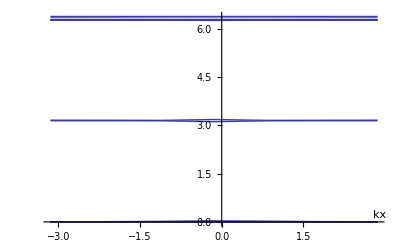

```mathematica
DiscretePlot[FCOr[kx],{kx,-Pi,Pi},Epilog->{Inset["kx",{Pi-0.25,0.2}],},Filling->None,Evaluate[Joined->True]]
```

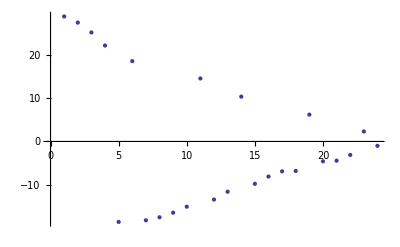

```mathematica
ListPlot[Re[N[Eigenvalues[CCor]]]]
```

```mathematica
Cor
```

2 (1+ⅇ^-ⅈ) π

```mathematica
Eigenvalues[Cor]
```

Eigenvalues::matsq: Argument {(2\ List\ π)[0, 2\ (1 + ⅇ^-ⅈ)\ π, 2\ π, 2\ π, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0], « 34 », 0[0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 2\ π, 0, 2\ (1 + ⅇ^-ⅈ)\ π, 0]} at position 1 is not a non-empty square matrix.

Eigenvalues[{(2 List π)[0,2 (1+ⅇ^-ⅈ) π,2 π,2 π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],(2 List π)[2 (1+ⅇ^ⅈ) π,0,2 π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],(2 List π)[2 π,2 π,0,2 (1+ⅇ^ⅈ) π,0,2 π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],(2 List π)[2 π,0,2 (1+ⅇ^-ⅈ) π,0,2 π,2 ⅇ^-ⅈ π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,2 π,0,2 (1+ⅇ^-ⅈ) π,2 π,2 π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,2 π,2 ⅇ^ⅈ π,2 (1+ⅇ^ⅈ) π,0,2 π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,2 π,2 π,0,2 (1+ⅇ^ⅈ) π,0,2 π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,2 π,0,2 (1+ⅇ^-ⅈ) π,0,2 π,2 ⅇ^-ⅈ π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,2 π,0,2 (1+ⅇ^-ⅈ) π,2 π,2 π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,2 π,2 ⅇ^ⅈ π,2 (1+ⅇ^ⅈ) π,0,2 π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,2 π,2 π,0,2 (1+ⅇ^ⅈ) π,0,2 π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,2 π,0,2 (1+ⅇ^-ⅈ) π,0,2 π,2 ⅇ^-ⅈ π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,2 π,0,2 (1+ⅇ^-ⅈ) π,2 π,2 π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,2 π,2 ⅇ^ⅈ π,2 (1+ⅇ^ⅈ) π,0,2 π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,2 π,2 π,0,2 (1+ⅇ^ⅈ) π,0,2 π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,2 π,0,2 (1+ⅇ^-ⅈ) π,0,2 π,2 ⅇ^-ⅈ π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,0,2 (1+ⅇ^-ⅈ) π,2 π,2 π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,2 ⅇ^ⅈ π,2 (1+ⅇ^ⅈ) π,0,2 π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,2 π,0,2 (1+ⅇ^ⅈ) π,0,2 π,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,0,2 (1+ⅇ^-ⅈ) π,0,2 π,2 ⅇ^-ⅈ π,0,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,0,2 (1+ⅇ^-ⅈ) π,2 π,2 π,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,2 ⅇ^ⅈ π,2 (1+ⅇ^ⅈ) π,0,2 π,0,0,0,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,2 π,0,2 (1+ⅇ^ⅈ) π,0,2 π,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,0,2 (1+ⅇ^-ⅈ) π,0,2 π,2 ⅇ^-ⅈ π,0,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,0,2 (1+ⅇ^-ⅈ) π,2 π,2 π,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,2 ⅇ^ⅈ π,2 (1+ⅇ^ⅈ) π,0,2 π,0,0,0,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,2 π,0,2 (1+ⅇ^ⅈ) π,0,2 π,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,0,2 (1+ⅇ^-ⅈ) π,0,2 π,2 ⅇ^-ⅈ π,0,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,0,2 (1+ⅇ^-ⅈ) π,2 π,2 π,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,2 ⅇ^ⅈ π,2 (1+ⅇ^ⅈ) π,0,2 π,0,0,0,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,2 π,0,2 (1+ⅇ^ⅈ) π,0,2 π,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,0,2 (1+ⅇ^-ⅈ) π,0,2 π,2 ⅇ^-ⅈ π,0,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,0,2 (1+ⅇ^-ⅈ) π,2 π,2 π],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,2 ⅇ^ⅈ π,2 (1+ⅇ^ⅈ) π,0,2 π,0],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,2 π,0,2 (1+ⅇ^ⅈ) π],0[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 π,0,2 (1+ⅇ^-ⅈ) π,0]}]

```mathematica
Cor[1][2][[1]][[2]]
```

2 (1+ⅇ^-ⅈ) π

```mathematica
Eigenvalues[Cor]
```

Eigenvalues::matsq: Argument {{{{0, 2\ (1 + ⅇ^-ⅈ)\ π, 2\ π, 2\ π}, {2\ (1 + ⅇ^ⅈ)\ π, 0, 2\ π, 0}, {2\ π, 2\ π, 0, 2\ (1 + ⅇ^ⅈ)\ π}, {2\ π, 0, 2\ (1 + ⅇ^-ⅈ)\ π, 0}}, « 7 », {{0, 2\ (1 + ⅇ^-ⅈ)\ π, 2\ π, 2\ π}, {2\ (1 + ⅇ^ⅈ)\ π, 0, 2\ π, 0}, {2\ π, 2\ π, 0, 2\ (1 + ⅇ^ⅈ)\ π}, {2\ π, 0, 2\ (1 + ⅇ^-ⅈ)\ π, 0}}}, {« 1 »}, {« 1 », « 7 », « 1 »}, {{« 1 »}, « 8 »}, {{« 1 »}, « 8 »}, {{« 1 »}, « 7 », {« 1 »}}, {« 1 »}, {« 1 »}, {« 1 »}} at position 1 is not a non-empty square matrix.

```mathematica
A=Table[i*j,{i,4},{j,4}]
```

{{1,2,3,4},{2,4,6,8},{3,6,9,12},{4,8,12,16}}

```mathematica
B=Table[0,{i,4},{j,4}]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
For[i=1,i≤4,i++,For[j=1,j≤4,j++,B[[i]][[j]]=A[[i]][[j]]]]
```

```mathematica
B
```

{{1,2,3,4},{2,4,6,8},{3,6,9,12},{4,8,12,16}}

```mathematica
Print[B]
```

{{1,2,3,4},{2,4,6,8},{3,6,9,12},{4,8,12,16}}

```mathematica
For[i=1,i≤4,i++,Print[i]]
```

1

2

3

4